## Init

```mathematica
NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
$root = NotebookDirectory[];
SetDirectory[$root];
$FKKSRoot = $root<>"../../../";
Import[$FKKSRoot<>"Packages/HelperFunctions.wl"]
```

## QNM Evaluator

```mathematica
Import[$root<>"nonR_master.wl"]
```

## Teukolsky Evaluator

```mathematica
<<HelperFunctions.wl
<<BHEvol.m
<<VectorFieldNorm.m
<<SpinWeightedSpheroidalHarmonics.m
<<RenormalizedAngularMomentum.m
<<MSTformalism.m
<<WeylPsi4.m
<<TeukolskyT.m
<<TeuInter.wl
```

```mathematica
Do[TeuCode[1,0,9/10,i,1], {i,0.3,0.3, 0.05}]//Timing
TeuInterEnv`out10["Derived"]["NormalizedEinf"]
```

Data import: 
	 input mass: 0.29999999999999998889776975374843459576`25.
	 data index: 130
	 mass: 0.3`25.
	 BH Spin: 0.9`25.
	 Mode: 1
	 Overtone: 0
	 Frequency: 0.2836323604304887114412526546297144404`25.150514992000527 + 0.00004648013512127190025526778527483182`21.365026594669114*I
	 Eigenvalue: -0.39559879999905111788218886039399384992`25. - 0.000042488056168004730408113187900236390910201415677367943`25.*I

Radsol[2]: 1.75195408134492396572290398003536340299`24.309764788531524 - 0.29566605197538973494809008774749484044`23.90858816434147*I

Angsol[2]: -3.14167824063605326892800150270855602179`25.149315318673548 + 3.0090690200578942157447138213657`18.13178206897535*^-7*I

precision: 25

rplus = 1.435889894354067355223698

rstart = 1.445889894354067355223698

epsilonr = 0.006964322291925094379954

rstop = 663.6666666666667160099122

r glue = 79.64

Interpolation: Start.

rmesh = 199

Thetamesh = 49

ThetaStart = 0.007767974743979812191074785

ThetaStop = 3.135539638126066286361038

Exponential extension: Start.

Solution at horizon: Test:

Rad[rtst] = 0.91754956614814094939564 - 0.43406856444505651984784 I

Exponential extension: Done!

Generating Interpolating functions for A_μ

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 1

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 2

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

General::stop: Further output of xAct`xTensor`PrintAsCharacter::argx will be suppressed during this calculation.

Data produced for: 3

Data produced for: 4

Interpolation: Done.

Adownvector[0,2,2,2] = {-0.901396, 1.14052, -0.487886, 4.67911}

Massnormalization: Start.

Tuptdownt test = -1.08935647138605729011828771036

sqrtmg test = 3.76474079784964483565743350856

rplus = 1.435889894354067355223698

rintstart = 1.44847914847200920362979559286

epsilonrint = 0.008767562309229220612865

rintstop = 680.388571127700199071585142442

thetastart = 0.007767974743979812191074785

thetastop = 3.135539638126066286361038

massNorm obtained: 2580.19074715450

Anorm obtained: 0.0033870180952792683819

Massnormalization: Done.

FindMinimum::reged: The point {4.8681,0.} is at the edge of the search region {0.,6.28319} in coordinate 2 and the computed search direction points outside the region.

Beginning Tlmω calculation

Subscript[T, μν] test: {{3.1387890680898495*^-6, 2.524932808994803*^-6, -7.823210544937628*^-7, -8.650371818318088*^-6}, {2.524932808994803*^-6, -0.00004076381591210996, 0.000011430967912895032, -0.000013407831419837934}, {-7.823210544937628*^-7, 0.000011430967912895032, 0.000014500972574110535, 4.310542103669997*^-6}, {-8.650371818318088*^-6, -0.000013407831419837934, 4.310542103669997*^-6, 0.000040093882036141686}}

TnnExpl Test: 4.855304377600522*^-8

rrange: {1.44588989435406735522369819838596156591`25., 1.4459228608042461999511838577163665271`25., 1.44606571542168786043695504814812135893`25.} ...

θrange: {0.00776797474397981219107478523255849723`25., 0.0716000495068795361537270913018170288`25., 0.13543212426977926011637939737107556038`25.} ...

---------------------------------------------------------------------

Generating: Tnn...

Generating: Tmn...

Generating: Tmm...

Generating: Done.

---------------------------------------------------------------------

Generating: Spheroidal harmonic for (s=-2,χ,Re(ω_Teu)).

Eigenvalues of SWSH: 2.43931678118436217945959

Generating: Interpolation data...

Generating: Tlmω.

Generating: Spheroidal harmonic for (s=-2,χ,Re(ω_Teu)).

Eigenvalues of SWSH: 9.21267727394496866308932

Generating: Interpolation data...

Generating: Tlmω.

Generating: Done.

---------------------------------------------------------------------

MST Solution (l=2, j=2)--------------------------------------

νsol[1]: 1.5`20. + 1.99432859529230066542027088871691375971`20.*I

1.5+0.70894327426231762423 ⅈ

νsol[2,2]: 0.5`19.91119774302928 + 0.70895546883103040294566055850564904215`20.062846695669943*I

AlmSWSH: 2.43931678118436217945959196775966559239`20.

λ_swsh: 0.65781308954696439076579224061558852371`19.430826516483673

Power::infy: Infinite expression 1/(0``-0.23434706931922658+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0``-0.23420348221868334+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0``-0.234203296270298+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

λ_(swsh,  MSTpackage): 0.6578130895469644

Rnumerical[2]: 1.09696 + 2.08265 I

SolR[2]: 0.1161550326049449786743588548924476697849348421835547452530678783 + 0.4424997410997615936638169965119625036401236323282034375670381238 I

Coeff: {PrivateMST`κ -> -0.19608236162207346 + 2.*I, PrivateMST`c1 -> 1.2536140440777088 + 0.9875259591342653*I, PrivateMST`c2 -> -0.4948390114406559 + 0.6125074983070338*I}

R0: -8.06502961510953775379261929239902498280812892913`19.937928311504336*^-11 - 1.039665669588311131805169191293876686958762355594`20.048216048562807*^-10*I

dR0: -0.00001409145643677660573674221435581121`19.877167632444575 - 0.00002237496430327696854317954044508528`20.077974101189408*I

norm: 2.45233544524245328233291729702614247798919677734375`100.04007737810824 + 1.9967114397078826737441659133764915168285369873046875`99.95081280891209*I

eqset: {(-0.6578130895469644 - (4.53811776688781938306004247407543104644`25.150514992000527*I)*PrivateMST`r + ((4*I)*(-1 + PrivateMST`r)*(-1.8 + 0.5672647208609775*(0.81 + PrivateMST`r^2)) + (-1.8 + 0.5672647208609775*(0.81 + PrivateMST`r^2))^2)/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2))*PrivateMST`R[PrivateMST`r] + (0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2*(-(((-2. + 2*PrivateMST`r)*Derivative[1][PrivateMST`R][PrivateMST`r])/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2) + Derivative[2][PrivateMST`R][PrivateMST`r]/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)) == 0, PrivateMST`R[1.43589989435406735522369819838596156591`20.] == -8.06502961510953775379261929239902498280812892913`19.937928311504336*^-11 - 1.039665669588311131805169191293876686958762355594`20.048216048562807*^-10*I, Derivative[1][PrivateMST`R][1.43589989435406735522369819838596156591`20.] == -0.00001409145643677660573674221435581121`19.877167632444575 - 0.00002237496430327696854317954044508528`20.077974101189408*I}

MST Solution (l=3, j=2)--------------------------------------

νsol[1]: 2.5`20. + 2.30268505469030770882454817183315753937`20.*I

2.595814934577721278

νsol[3,2]: 2.59606573686375676608761565995696639282`20.

AlmSWSH: 9.21267727394496866308932272265329866594`20.

λ_swsh: 6.41009708475781151320701343884224961181`19.842475864779317

λ_(swsh,  MSTpackage): 7.431173582307571

Rnumerical[2]: 1.42447 + 0.969446 I

SolR[2]: -0.0541045241136465067048105195080542057960459468088774049597563153 + 0.1628800025534721169465457319064336281970424443629709224563889466 I

Coeff: {PrivateMST`κ -> -0.19608236162207346 + 2.*I, PrivateMST`c1 -> 3.4734677266503677 + 0.697343190778063*I, PrivateMST`c2 -> 3.040570915586129 + 1.656147155301655*I}

R0: -8.06526958686940588727504362275058276170999539037`19.93793017504036*^-11 - 1.039689458516744858591665447583889693388548902174`20.048214927150532*^-10*I

dR0: -0.00001409212970848763162891266047506719`19.87717191715118 - 0.0000223757250313031771688754894662108`20.07797240171693*I

norm: 0.81612140970000168760378755905549041926860809326171875`100.11756189857377 + 0.330377621488630257573504422907717525959014892578125`99.72481774971945*I

eqset: {(-7.431173582307571 - (4.53811776688781938306004247407543104644`25.150514992000527*I)*PrivateMST`r + ((4*I)*(-1 + PrivateMST`r)*(-1.8 + 0.5672647208609775*(0.81 + PrivateMST`r^2)) + (-1.8 + 0.5672647208609775*(0.81 + PrivateMST`r^2))^2)/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2))*PrivateMST`R[PrivateMST`r] + (0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2*(-(((-2. + 2*PrivateMST`r)*Derivative[1][PrivateMST`R][PrivateMST`r])/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2) + Derivative[2][PrivateMST`R][PrivateMST`r]/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)) == 0, PrivateMST`R[1.43589989435406735522369819838596156591`20.] == -8.06526958686940588727504362275058276170999539037`19.93793017504036*^-11 - 1.039689458516744858591665447583889693388548902174`20.048214927150532*^-10*I, Derivative[1][PrivateMST`R][1.43589989435406735522369819838596156591`20.] == -0.00001409212970848763162891266047506719`19.87717191715118 - 0.0000223757250313031771688754894662108`20.07797240171693*I}

MST Solution (l=4, j=2)--------------------------------------

νsol[1]: 3.5`20. + 1.948794120898588611012769433727953583`20.*I

3.7064484559408739095

νsol[4,2]: 3.70655707310100095946230766245449998907`20.

AlmSWSH: 17.49993954320642540430879864644112596255`20.

λ_swsh: 13.67628285646950889323797980596310492298`19.89292957490637

λ_(swsh,  MSTpackage): 15.718435851569028

Rnumerical[2]: 4.6493 + 1.92874 I

SolR[2]: -0.0368781544093923963164354933092890598011136737122929977071690038 + 0.1378450888967023452785629714990887316786832825382020110724895454 I

Coeff: {PrivateMST`κ -> -0.19608236162207346 + 2.*I, PrivateMST`c1 -> 6.18947696409281 + 0.34230218713467564*I, PrivateMST`c2 -> 12.365687196436335 + 1.774498357694993*I}

R0: -8.06556320118144422004970866372670063870530132668`19.93793245503084*^-11 - 1.039718565027298133831236886655615759822105704098`20.048213555109236*^-10*I

dR0: -0.00001409295348842431723225738342800759`19.877177159256025 - 0.00002237665581208938970645202449371977`20.077970322441345*I

norm: 0.886454035129445205853926381678320467472076416015625`100.1276555561174 + 0.29535331768162020882328988591325469315052032470703125`99.65034118847596*I

eqset: {(-15.718435851569028 - (4.53811776688781938306004247407543104644`25.150514992000527*I)*PrivateMST`r + ((4*I)*(-1 + PrivateMST`r)*(-1.8 + 0.5672647208609775*(0.81 + PrivateMST`r^2)) + (-1.8 + 0.5672647208609775*(0.81 + PrivateMST`r^2))^2)/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2))*PrivateMST`R[PrivateMST`r] + (0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2*(-(((-2. + 2*PrivateMST`r)*Derivative[1][PrivateMST`R][PrivateMST`r])/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2) + Derivative[2][PrivateMST`R][PrivateMST`r]/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)) == 0, PrivateMST`R[1.43589989435406735522369819838596156591`20.] == -8.06556320118144422004970866372670063870530132668`19.93793245503084*^-11 - 1.039718565027298133831236886655615759822105704098`20.048213555109236*^-10*I, Derivative[1][PrivateMST`R][1.43589989435406735522369819838596156591`20.] == -0.00001409295348842431723225738342800759`19.877177159256025 - 0.00002237665581208938970645202449371977`20.077970322441345*I}

GW Power --------------------------------------

Mode: {2, 2}

221.2222222222222386699707

2.445889894354067355223698

Eigenvalues of SWSH: 2.43931678118436217945959

Psi4(r->Inf): Done.

Total GW energy flux: Done.

Mode: {3, 2}

221.2222222222222386699707

2.445889894354067355223698

Eigenvalues of SWSH: 9.21267727394496866308932

Psi4(r->Inf): Done.

Total GW energy flux: Done.

{450.606,Null}

0.0000549414813

```mathematica
TeuInterEnv`out10["Derived", "Einf"]
```

4.81364501×10^-8

Comparison of EM Projections

```mathematica
With[{T=20, R=1},
Column[{
Row[{"TnnInter: \n\t"<>ToString[TnnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TnnInter]: \n\t"<>ToString[Derivative[1,0][TnnInter][T,R], InputForm]}],
Row[{"TmnInter: \n\t"<>ToString[TmnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmnInter]: \n\t"<>ToString[Derivative[1,0][TmnInter][T,R], InputForm]}],
Row[{"TmmInter: \n\t"<>ToString[TmmInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmmInter]: \n\t"<>ToString[Derivative[1,0][TmmInter][T,R], InputForm]}]
}]
]
```

Comparison of Teukolsky Source Term

```mathematica
TeukolskyTintegrandExpl[20,1]
```

Comparison of SWSH

```mathematica
PrivateTeukolsky`SWSHS[2][1]
```

Comparison of Teukolsky integrand

```mathematica
teukint = {r,θ}|->TeukolskyTintegrandExpl[r,θ]*Sin[θ]*PrivateTeukolsky`SWSHS[2][θ];
teukint[20,1]
```

Comparison of Tlmω

```mathematica
Tlmω[2][3.86]
```

0.0269807-0.0434692 ⅈ

Comparison of Renormalized angular momentum

```mathematica
TeuInterEnv`νsolIn[2,2][2*TeuInterEnv`wr]
```

Comparison of Homogeneous solution of MST

```mathematica
With[{TeuInterEnv`spinin=0.9,TeuInterEnv`wr=0.2836323604304887114412526546297144404`25.150514992000527,TeuInterEnv`rstop = 400},
MSTgRoots[TeuInterEnv`spinin,-2,2,2,2];
νsol[w_]:=nufullBHPT[w];
MSTSolution[TeuInterEnv`spinin,νsol[2*TeuInterEnv`wr],2*TeuInterEnv`wr,AlmSWSH[2*TeuInterEnv`wr], -2,2,2,TeuInterEnv`rstop];
MSTformalism`Rnumerical[2]
]
```

Power::infy: Infinite expression 1/(0``-0.24492676912543812+0. ⅈ) encountered.

Comparison of Z_lmω integrand

```mathematica
tlmw = TeuInterEnv`Tlmω[2];
Rin = {TeuInterEnv`r}|->TeuInterEnv`RinSet[2,2]//Evaluate;
integrand = {r}|->tlmw[r]*Rin[r]/((r^2-2*r+(0.9)^2)^2);
integrand[3.86]
```

0.00114555+0.0666244 ⅈ

Comparison of incoming amplitude

```mathematica
TeuInterEnv`BincSet[2,2]
```

15.557757115769586849-1.268787830754477098 ⅈ

Comparison of Z_lmω

```mathematica
integration = NIntegrate[integrand[rr]//Re,{rr,TeuInterEnv`rstart+1,TeuInterEnv`rstop},MaxRecursion->50,WorkingPrecision->10]
zinf = integration/(2 * I * 2*TeuInterEnv`wr * TeuInterEnv`BincSet[2,2])
```

-0.005281250589

-0.0000242402517+0.000297231687 ⅈ

```mathematica
integrand[5]
```

-0.142085+0.0844879 ⅈ

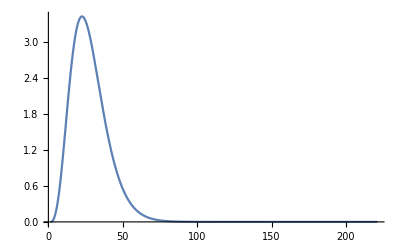

```mathematica
Plot[integrand[r]//Abs, {r,TeuInterEnv`rstart,TeuInterEnv`rstop}, PlotRange->All]
```